# Quantum Phase Estimation Algorithm

We will discuss the Quantum Phase Estimation (QPE) algorithm. This algorithm estimates the eigenvlaues of a unitary by applying controlled powers of it to an eigenstate, imprinting the phase on ancilla qubits, then using the inverse quantum Fourier transform to read out a binary approximation; precision scales with the number of ancillas, enabling applications like factoring and eigenvalue estimation.

## Key Concepts

Eigenvalue

Eigenvector

Quantum Fourier Transform

## Eigenvectors and Eigenvalues

Eigenvectors and eigenvalues are concepts from the theory of linear algebra, and they are frequently used in analyzing the solutions of all sorts of mathematical models.

From linear algebra and the theory of matrices, you should recall that an n×n matrix acting on an n dimensional vector will give another n dimensional vector. In the case of real numbers, it is only the case that a x=b x if a=b or x=0. For square matrices, it is possible to have A x⃗=λ x⃗ for a real number, λ. When this happens x⃗ is called an eigenvector of A and λ is the corresponding eigenvalue of A.

As an example, consider the matrix corresponding to the Pauli Z operator in the computational basis:

```mathematica
PauliMatrix[3]//MatrixForm
```

(1 | 0
0 | -1)

You can compute the eigenvalues and eigenvectors of this matrix using the Eigensystem function:

```mathematica
Eigensystem[PauliMatrix[3]]
```

{{-1,1},{{0,1},{1,0}}}

These are the lists of eigenvalues followed by the eigenvectors. Let’s look at them in the form λ_i->(x⃗)_i:

```mathematica
QuantumOperator["Z"]["Eigensystem"]//MapThread[Rule]
```

{-1→{0,1},1→{1,0}}

You can see from the eigenvectors that the state 0 corresponds to the positive eigenvalue of the Pauli Z operator. Similarly, the state 1 corresponds to the negative eigenvalue of the Pauli Z operator. That’s the conventional we also use to define the computational basis:

```mathematica
QuantumBasis["Computational"]["ElementAssociation"]
```

<|0→{1,0},1→{0,1}|>

If a matrix is Hermitian (i.e., H=H^†) then its eigenvalues are always real. For example, matrices drawn from GaussianUnitaryMatrixDistribution are Hermitian:

```mathematica
h=RandomVariate[GaussianUnitaryMatrixDistribution[9]];
```

Check the matrix is Hermitian:

```mathematica
HermitianMatrixQ[h]
```

True

Check all eigenvalues are Real:

```mathematica
Eigenvalues[h]∈Reals
```

True

## Quantum Phase Estimation

Gate operators in a quantum circuit can be represented as unitary matrices. A unitary matrix is defined by the property that U^†=U^-1. In Wolfram Language, this is equivalent to ConjugateTranspose[U]==Inverse[U].

For example, let’s check that Pauli operators are unitary:

```mathematica
Table[ConjugateTranspose[PauliMatrix[j]]==Inverse[PauliMatrix[j]],{j,3}]
```

{True,True,True}

Of course, there is also a direct way of checking unitarity in the Wolfram Language:

```mathematica
Table[UnitaryMatrixQ[PauliMatrix[j]],{j,3}]
```

{True,True,True}

For a unitary matrix, its eigenvalues are of the form Uλ=ⅇ^(2π ⅈ θ)λ for a real number θ. Let’s explore this feature explicitly.

Let’s consider such a random unitary matrix:

```mathematica
SeedRandom[1234];
Urandom=QuantumOperator["RandomUnitary"]
```

QuantumOperator[…]

Remember that any random generation follows a specific distribution. Here, the random unitaries are sampled uniformly from the unitary group (the Haar measure over n-dimensional unitary matrices).

Given above random unitary operator, let’s obtain its eigenvalues:

```mathematica
λs=Urandom["Eigenvalues"]
```

{0.429566+0.903035 ⅈ,-0.645446-0.763806 ⅈ}

Find each θ such that λ=ⅇ^(2π ⅈ θ):

```mathematica
θs=Mod[Arg[λs]/(2Pi),1]
```

{0.179333,0.638336}

Check the relation:

```mathematica
λs==Exp[2 Pi I θs]
```

True

So far we computed eigenvalues classically. Quantum Phase Estimation (QPE) uses phase kickback to extract the eigenstate’s phase, providing the information needed to recover the eigenvalues.

First, let’s obtain the QPE circuit for this unitary operator:

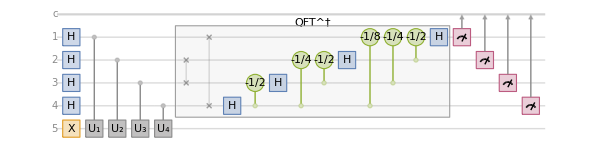

```mathematica
qc1=QuantumCircuitOperator["PhaseEstimation"[Urandom]];
qc1["Diagram",ImageSize->600]
```

Notice a few things about the circuit. First, the first four qubits are put into a uniform superposition, then used as control qubits, then acted on by the inverse quantum Fourier transform, finally measured. Lastly, the fifth qubit is put into the state 1 and then acted on by a sequence of four conditional gates, where each of its unitary operator is simply a power of the unitary matrix you began with.

Through this procedure, the base-2 digits of θ will be encoded in the register qubits. Observe what happens when the circuit is run:

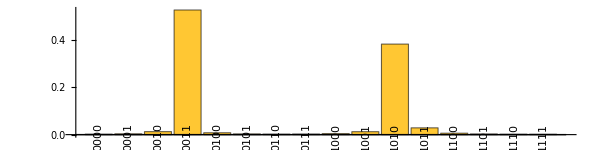

```mathematica
measurements1=N[qc1][];
measurements1["ProbabilityPlot",]
```

The measurement probabilities are strongly peaked around two particular results. These results represent estimates of the values of θ:

```mathematica
results1=KeySort@TakeLargest[measurements1["Probabilities"],2]
```

<|0011→0.526029,1010→0.382148|>

```mathematica
KeyMap[#["Name"]&]@results1
```

<|{0,0,1,1}→0.526029,{1,0,1,0}→0.382148|>

These results can be read as the binary representation of a number between 0 and 1-2^-n, where n was the number of register qubits. In this case, there were four register qubits.

```mathematica
estimates1=Map[FromDigits[#["Name"],2]/2^Length[#["Name"]]&,Keys@results1]
```

{3/16,5/8}

Compare these estimates to the actual values for θ:

```mathematica
θs==Around[estimates1,2^-4]
```

True

QPE precision scales with the number of “phase” qubits. Roughly, every extra phase qubit buys you one extra bit of phase precision, i.e. resolution ≈2^-n
 if you use n phase qubits. The default here is 4, but you can increase or decrease it as needed.

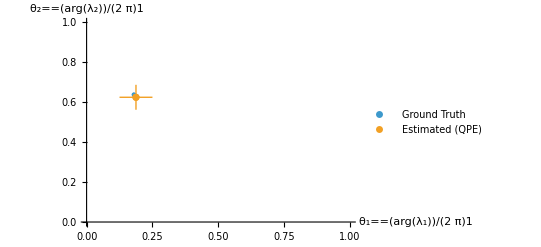

```mathematica
ListPlot[{{θs},{Around[estimates1,2^-4]}},]
```

Within the resolution given by δ=2^-n, the algorithm finds states 2^n x such that x-δ≤θ≤x+δ. Critically, this was done without ever inverting the matrix U. Instead of the classical computational costs of inverting the matrix, you must apply O(n^2) powers of the matrix U in order to obtain resolution δ=2^-n. This comes from the fact that ∑_(k=1)^n k=n(n+1)/2.

## Phase Estimation with Larger Matrices

Consider a larger 4×4 matrix which acts on 2 qubits:

```mathematica
SeedRandom[1234];
Urandom2=QuantumOperator["RandomUnitary"[2,2]]
```

QuantumOperator[…]

This time, there are four eigenvalues:

```mathematica
λ2=Urandom2["Eigenvalues"]
```

{-0.710774-0.70342 ⅈ,0.82902+0.559219 ⅈ,-0.990375-0.138413 ⅈ,0.503335-0.864091 ⅈ}

Find each θ such that λ=ⅇ^(2π ⅈ θ):

```mathematica
θ2=Mod[Arg[λ2]/(2Pi),1]
```

{0.624172,0.0944495,0.5221,0.833947}

Check the relation:

```mathematica
λ2==Exp[2 Pi I θ2]
```

True

Obtain the circuit for this larger unitary operator but this time with 5 phase qubits:

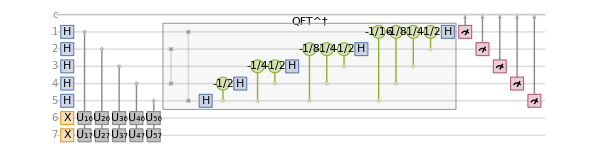

```mathematica
qc2=QuantumCircuitOperator["PhaseEstimation"[Urandom2,5]];
qc2["Diagram",ImageSize->600]
```

This time, two ancilla qubits are needed so that the 4×4 unitary can act properly on the circuit. Other than this difference, the circuit works following the same principles as before. Controlled operators (corresponding to powers of the matrix under consideration) are used to encode information about the operator’s eigenvalues into the phases of the register qubits. This information is then decoded by measuring the register qubits.

Execute the circuit:

```mathematica
measurements2=N[qc2][];
```

Plot the probabilities:

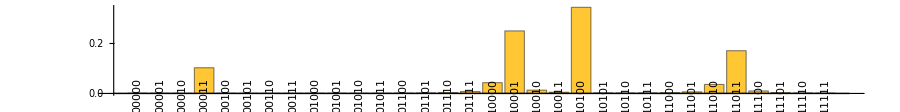

```mathematica
measurements2["ProbabilityPlot",AspectRatio->1/8,ImageSize->900,"LabelsAngle"->90 °]
```

Unlike the previous case, it is not so obvious which of these measurement results are supposed to correspond to the four eigenvalues. Let’s proceed with the four most likely outcomes and hope for the best:

```mathematica
results2=KeySort@TakeLargest[measurements2["Probabilities"],4]
```

<|00011→0.101013,10001→0.245791,10100→0.338453,11011→0.168005|>

Compute the estimates based on the four most likely outcomes:

```mathematica
estimates2=Map[FromDigits[#,2]/(2^Length[#])&,First/@Keys@results2]
```

{3/32,17/32,5/8,27/32}

This time, the actual values for θ were not all captured by the four most likely outcomes:

```mathematica
Sort[θ2]==Around[estimates2,2^-5]
```

True

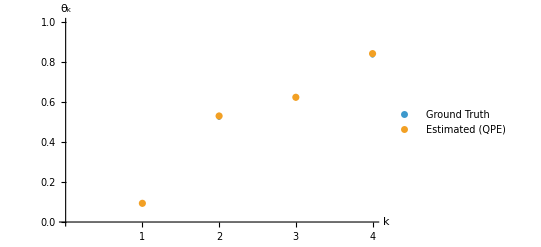

```mathematica
ListPlot[{Sort@θ2,Around[estimates2,2^-6]},]
```

While the applications are beyond the scope of this lesson, efficient computation of matrix eigenvalues allows many shortcuts in understanding the stability and solution space of a wide range of quantitative models. For more on the uses of eigenvalues and eigenvectors, see the Introduction to Linear Algebra.

## Initialization

Install Wolfram quantum framework

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]